## Tupik_D_L

## Lab_work_8: Работа с БД в Wolfram Mathematica. Wolfram Alpha

## Работа с БД

```mathematica
connection = DatabaseReference["postgresql://postgres@localhost:5432/lab045"]
```

DatabaseReference[…]

```mathematica
DatabaseConnect[connection]
```

DatabaseConnect[connection]

```mathematica
connection [{"Name","ID"}]
```

<|Name→lab045,ID→1xiwncnb1ftxj|>

```mathematica
bdObject=RelationalDatabase[connection ]
```

RelationalDatabase[…]

```mathematica
entity=EntityStore[bdObject]
```

EntityStore[…]

```mathematica
EntityRegister[entity]
```

{students,lecturers,univercities,subjects,exam_marks,subj_lect}

```mathematica
EntityValue[ 
	"univercities",
	{"univ_id","univ_name", "city"},
	"Dataset"
]
```

```mathematica
ExternalEvaluate[connection,"SELECT * FROM exam_marks WHERE subj_id = 201"]
```

```mathematica
DatabaseDisconnect[connection]
```

Success[…]

## Wolfram Alpha

```mathematica
WolframAlpha["Belarus"]
```

WolframAlphaQueryResults

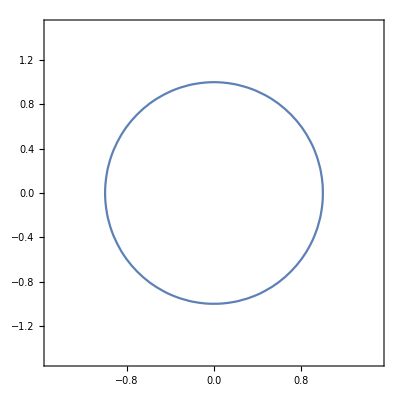

```mathematica
ContourPlot[x^2 + y^2 == 1, {x, -3/2, 3/2}, {y, -3/2, 3/2}]
```

WolframAlphaQueryParseResults

-Graphics-

-Graphics-

red square

WolframAlphaQueryResults

```mathematica
WolframAlpha["Brest", "Image"]
```

-Graphics-

```mathematica
WolframAlpha["Brest population", "SpokenResult"]
```

In 2016, the population of Brest, Brest, was about 340141 people

water

WolframAlphaQueryResults

Fresnel equations

WolframAlphaQueryResults